## data

data sources are from FRED 

use url

https://fred.stlouisfed.org/series/[data label]

e.g.

https://fred.stlouisfed.org/series/TB3MS

for the 3-month secondary market rate

```mathematica
minyear=1960.0;
maxyear=2017.0;
```

```mathematica
(*
gdp={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+0.25,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\GDP.xls"][[1]],11];
GDP=Interpolation[gdp,InterpolationOrder->1];
*)

(* here, using gross private domestic investment GPDI instead of GDP *)

gdp={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+0.25,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\GPDI.xls"][[1]],11];
GDP=Interpolation[gdp,InterpolationOrder->1];
```

```mathematica
mb={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+1/12.,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\AMBSL.xls"][[1]],11];
MB=Interpolation[mb,InterpolationOrder->1];
```

```mathematica
r03={1900+FromDate[Normal[#[[1]]]]/(365.24*3600*24)+1/12.,#[[2]]}&/@Drop[Import["C:\\Users\\dp864c\\Desktop\\SAVED DESKTOP\\TB3MS.xls"][[1]],11];
R03=Interpolation[r03,InterpolationOrder->1];
```

## fit

```mathematica
solution=FindMinimum[Total[Table[Abs[(xx Log[GDP[yy]/MB[yy]]+zz)-Log[R03[yy]]],{yy,minyear,maxyear,1/12.}]],{{xx,3.0},{zz,-10.0}},Method->"PrincipalAxis"]
X0=xx/.solution[[2]];
Z0=zz/.solution[[2]];
```

{266.502,{xx→3.15255,zz→-2.02646}}

### graph

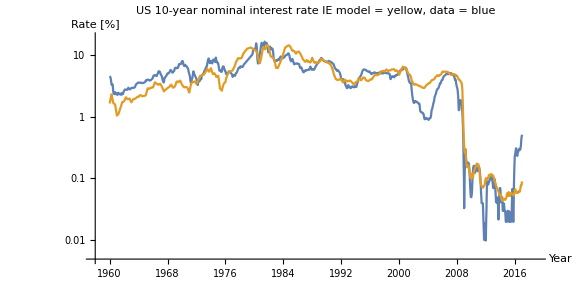

```mathematica
Show[LogPlot[{R03[yy],Exp[(X0 Log[GDP[yy]/MB[yy]]+Z0)]},{yy,minyear,maxyear},BaseStyle->{FontSize->13},Axes->True,ImageSize->Large,Frame->False,AspectRatio->1/2,PlotRange->{{minyear-2,maxyear+2},{0.005,19}},AxesLabel->{"Year "," Rate [%]"},PlotLabel->"\nUS 10-year nominal interest rate\nIE model = yellow, data = blue"]]
```